```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
Needs["PlotLegends`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\analysis-mirror_neutrons\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar\\runs2"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/analysis-mirror_neutrons/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadesc={Number,Number,Number,Number,Number,Number,Number,Word,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,seperator,"desctf_c.dat"],metadesc];
dimdesc=Dimensions[descdat][[1]];
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Working Directory: C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\runs2

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

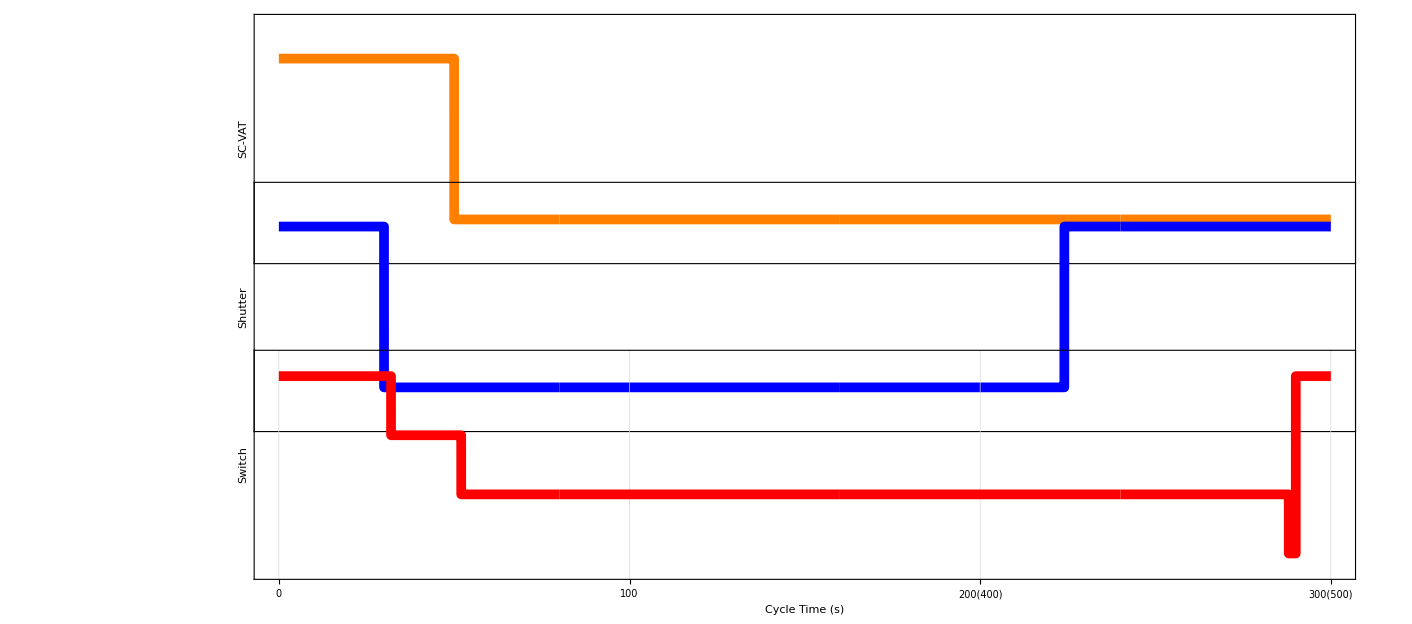

```mathematica
vat=Table[{k,If[k<50,1,-1]},{k,0,300,.01}];
shutter=Table[{k,If[k<30||k>224,1,-1]},{k,0,300,.01}];
switch=Table[{k,If[k<32||k>290,1.2,If[k>=32&&k<=52,.4,If[k>52&&k<288,-.4,-1.2]]]},{k,0,300,.01}];
one=ListLinePlot[vat,PlotRange->{{-1,301},{-1.49,1.49}},PlotStyle->{Orange,Thickness[.005]},Frame->True,FrameLabel->{"","SC-VAT"},FrameTicks->
{{None,{{-1,"Closed",{0.02,0}},{1,"Open",{0.02,0}}}},{None,{{0,"0",{0.02,0}},{100,"100",{0.02,0}},{200,"200(400)",{0.02,0}},{300,"300(500)",{0.02,0}}}}},
TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->1400,AspectRatio->1/4,Axes->None,GridLines->Automatic];
two=ListLinePlot[shutter,PlotRange->{{-1,301},{-1.49,1.49}},PlotStyle->{Blue,Thickness[.005]},Frame->True,FrameLabel->{"","Shutter"},FrameTicks->{{None,{{-1,"Closed",{0.02,0}},{1,"Open",{0.02,0}}}},{None,None}},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->1400,AspectRatio->1/4,Axes->None,GridLines->Automatic];
three=ListLinePlot[switch,PlotRange->{{-1,301},{-1.49,1.49}},PlotStyle->{Red,Thickness[.005]},Frame->True,FrameLabel->{"Cycle Time (s)","Switch"},FrameTicks->{{None,{{1.2,"Filling",{0.02,0}},{0.4,"Monitor",{0.02,0}},{-0.4,"Empty",{0.02,0}},{-1.2,"Pump",{0.02,0}}}},{{{0,"0",{0.02,0}},{100,"100",{0.02,0}},{200,"200(400)",{0.02,0}},{300,"300(500)",{0.02,0}}},None}},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->1400,AspectRatio->1/4,Axes->None,GridLines->Automatic];
GraphicsGrid[{{Show[one,ImagePadding->{{40,110},{80,40}}]},{Show[two,ImagePadding->{{40,110},{80,40}}]},{Show[three,ImagePadding->{{40,110},{80,40}}]}},Spacings->{0,-146},AspectRatio->Full]
```

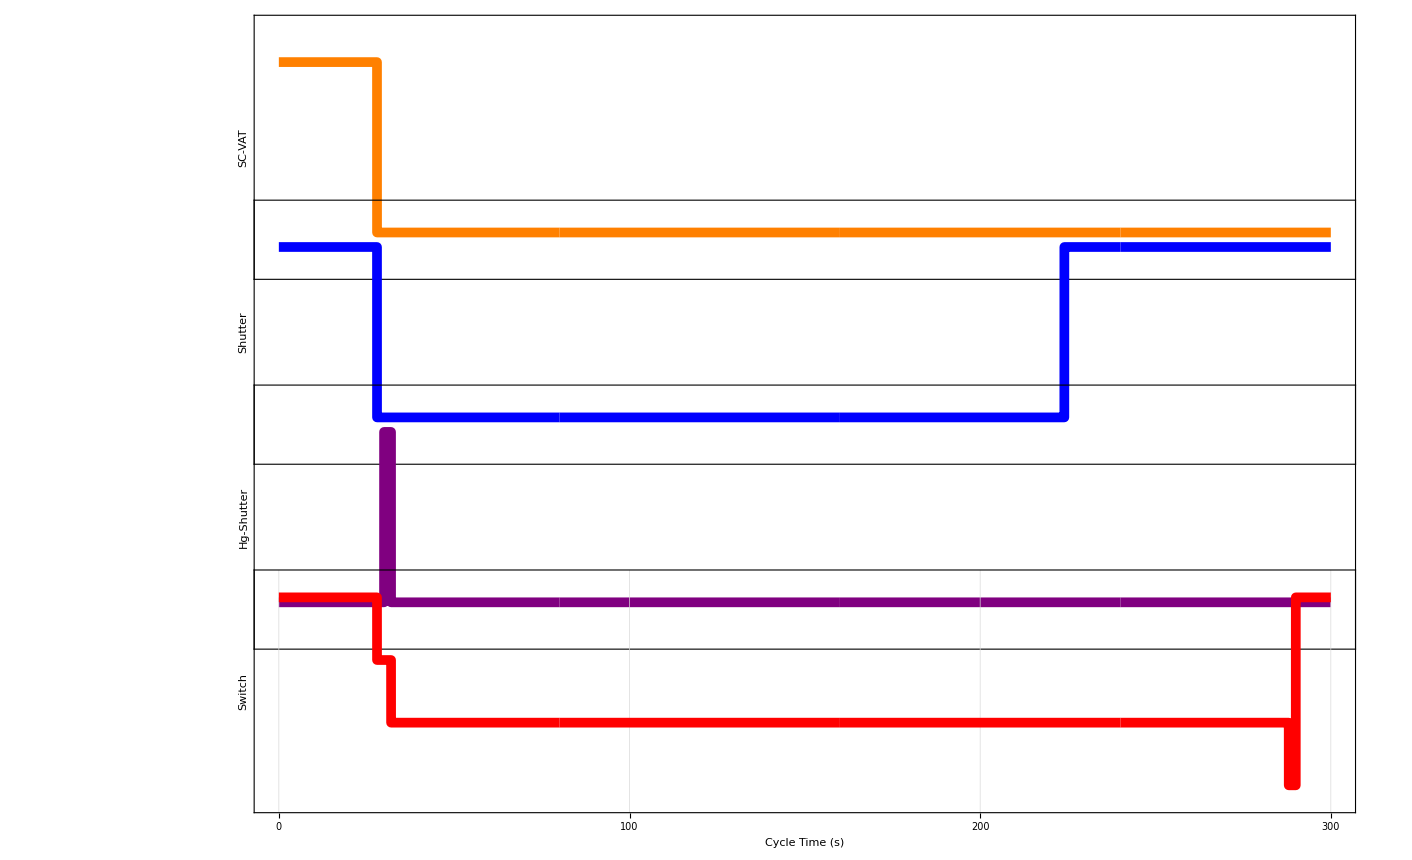

```mathematica
vat=Table[{k,If[k<28,1,-1]},{k,0,300,.01}];
shutter=Table[{k,If[k<28||k>224,1,-1]},{k,0,300,.01}];
hg=Table[{k,If[k<32&&k>30,1,-1]},{k,0,300,.01}];
switch=Table[{k,If[k<28||k>290,1.2,If[k≥28&&k≤32,.4,If[k>32&&k<288,-.4,-1.2]]]},{k,0,300,.01}];
one=ListLinePlot[vat,PlotRange->{{-1,301},{-1.49,1.49}},PlotStyle->{Orange,Thickness[.005]},Frame->True,FrameLabel->{"","SC-VAT"},FrameTicks->
{{None,{{-1,"Closed",{0.02,0}},{1,"Open",{0.02,0}}}},{None,{{0,"0",{0.02,0}},{100,"100",{0.02,0}},{200,"200",{0.02,0}},{300,"300",{0.02,0}}}}},
TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->1400,AspectRatio->1/4,Axes->None,GridLines->Automatic];
two=ListLinePlot[shutter,PlotRange->{{-1,301},{-1.49,1.49}},PlotStyle->{Blue,Thickness[.005]},Frame->True,FrameLabel->{"","Shutter"},FrameTicks->{{None,{{-1,"Closed",{0.02,0}},{1,"Open",{0.02,0}}}},{None,None}},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->1400,AspectRatio->1/4,Axes->None,GridLines->Automatic];
four=ListLinePlot[hg,PlotRange->{{-1,301},{-1.49,1.49}},PlotStyle->{Purple,Thickness[.005]},Frame->True,FrameLabel->{"","Hg-Shutter"},FrameTicks->{{None,{{-1,"Closed",{0.02,0}},{1,"Open",{0.02,0}}}},{None,None}},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->1400,AspectRatio->1/4,Axes->None,GridLines->Automatic];
three=ListLinePlot[switch,PlotRange->{{-1,301},{-1.49,1.49}},PlotStyle->{Red,Thickness[.005]},Frame->True,FrameLabel->{"Cycle Time (s)","Switch"},FrameTicks->{{None,{{1.2,"Filling",{0.02,0}},{0.4,"Monitor",{0.02,0}},{-0.4,"Empty",{0.02,0}},{-1.2,"Pump",{0.02,0}}}},{{{0,"0",{0.02,0}},{100,"100",{0.02,0}},{200,"200",{0.02,0}},{300,"300",{0.02,0}}},None}},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->1400,AspectRatio->1/4,Axes->None,GridLines->Automatic];
GraphicsGrid[{{Show[one,ImagePadding->{{40,110},{80,40}}]},{Show[two,ImagePadding->{{40,110},{80,40}}]},{Show[four,ImagePadding->{{40,110},{80,40}}]},{Show[three,ImagePadding->{{40,110},{80,40}}]}},Spacings->{0,-138},AspectRatio->Full]
```